```mathematica
<<Data`;
<<BISFit`;
Names["BISfit`*"]
```

{BISffit,BISffitxy,BISLSfit,BISLSfitxy,ColeP,ColePxy,Filterd,LSfit,Maxd,Mind}

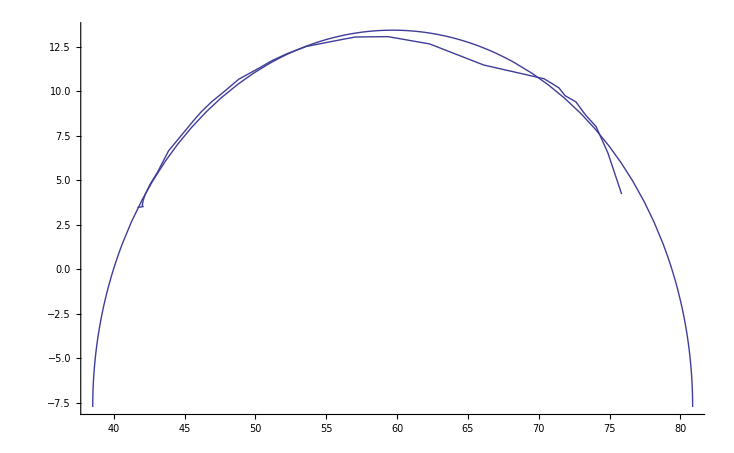
```mathematica
(*the circle is:*)
(*r0=m-√(r^2-n^2)/.sol
r1=m+√(r^2-n^2)/.sol
a=2/π ArcCos[-n/r]/.sol//N

l=Length[X];

F[m_,n_,r_]=∑_(k=1)^l ((X[[k]]-m)^2+(Y[[k]]-n)^2-r^2)^2/.sol*)

(*{m,n,r}={m,n,r}/.sol
Show[p0,ParametricPlot[{r Cos[th]+m,r Sin[th]+n},{th,0,π}]]*)
(*{m->59.68860688710969,n->-7.741046298168661,r->21.17640156634635}*)
{59.68860688710969,-7.741046298168661,21.17640156634635}
-Graphics-
(*FindFit[Z,{y0+√(r2-(xx-x0)^2),r2-(xx-x0)^2⩾0},{{y0,5},{r2,3600},{x0,55}},xx]
nlm=NonlinearModelFit[Z,Log[a +b x^2],{a,b},x]*)
```

```mathematica
(*ListPlot[data0[[All,2]]]*)
p0=ListPlot[Z,Joined->True]
ListPlot[{freq/100,data0[[All,1]]}]
```

```mathematica
(*test freq calculation*)
d=xyData[data[[1,All,{1,2}]]];

{m,n,R}=BISffit[data[[1,All,{1,2}]]];
{r0,r1,a,fc}=ColeP[data[[1,All,{1,2}]],f]
```

```mathematica
α=a;
rc[f_]:=r1+(r0-r1)/(1+(ⅈ f/fc2)^α);
```

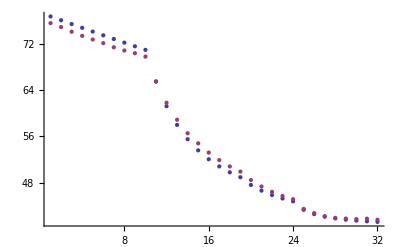

8504.28

8504.28

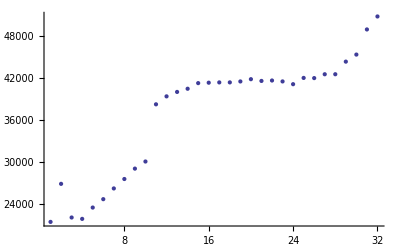

-Graphics-

```mathematica
ListPlot[{Re[Map[rc,f]],RR}]
dfc=Table[-Re[ f[[i]]Re[ⅈ((XX[[i]]ⅈ+RR[[i]]-r1)/(r0-XX[[i]]ⅈ-RR[[i]]))^(1/a)]],{i,1,32}];

dfc2=Table[-Re[ f[[i]]ⅈ((XX[[i]]ⅈ+RR[[i]]-r1)/(r0-XX[[i]]ⅈ-RR[[i]]))^(1/a)],{i,1,32}];
StandardDeviation[dfc]
StandardDeviation[dfc2]
ListPlot[Table[-Re[f[[i]]Im[-((XX[[i]]ⅈ+RR[[i]]-r1)/(r0-XX[[i]]ⅈ-RR[[i]]))^(1/a)]],{i,1,32}]]
ListPlot[Table[-Re[f[[i]]ⅈ((XX[[i]]ⅈ+RR[[i]]-r1)/(r0-XX[[i]]ⅈ-RR[[i]]))^(1/a)],{i,1,32}]]
```

```mathematica
(*new data are different anyway*)
```

```mathematica
alldata=nxrData[5];
ff=Freq[];
```

```mathematica
Dimensions[alldata[[5]]]
```

{1,6,23,2}

```mathematica
pr1=alldata[[3]];
pr2=alldata[[4]];
pr1t1=pr1[[1]];
pr2t1=pr2[[1]];
```

```mathematica
h1=pr1t1[[2]]
```

{{2146.15,845.823},{2079.73,909.478},{2079.7,856.767},{2037.93,810.166},{2038.77,765.917},{2024.1,731.118},{2012.65,680.852},{1995.22,658.698},{1997.7,627.19},{1969.93,585.766},{1947.14,544.384},{1922.67,514.1},{1918.95,504.143},{1918.4,472.624},{1906.48,457.353},{1912.07,434.762},{1895.04,413.879},{1899.2,407.847},{1907.04,366.548},{1911.29,379.139},{1895.9,369.213},{1880.36,348.843},{1885.86,318.631}}

```mathematica
(*will this fitted into a circle??*)
```

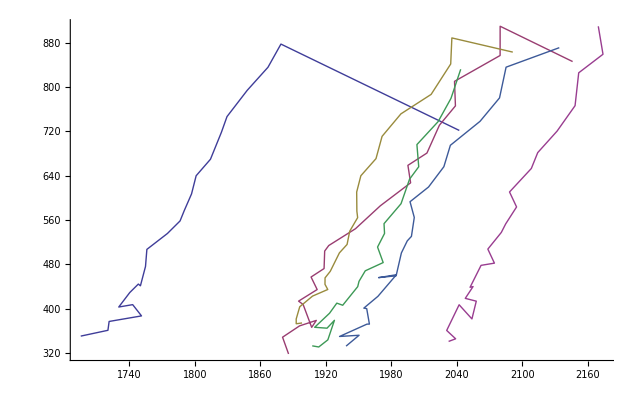

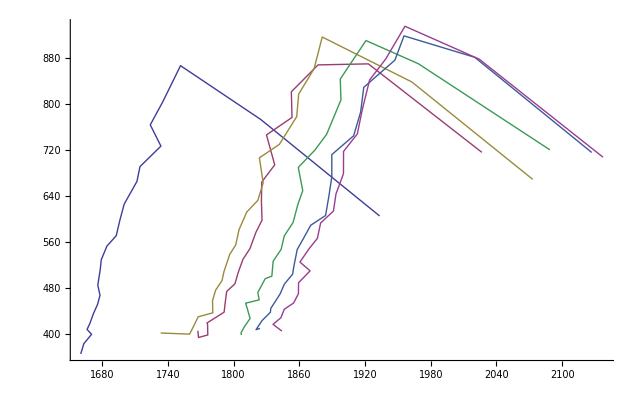

```mathematica
ListPlot[pr1t1,Joined->True]
ListPlot[pr2t1,Joined->True]
```

```mathematica
ff
```

{34000,37000,40000,43000,46000,49000,52000,55000,58000,61000,64000,67000,70000,73000,76000,79000,82000,85000,88000,91000,94000,97000,100000}

```mathematica
ColePxy[h1,ff]//Timing
{m,n,r}=BISLSfitxy[h1]
```

{2.75387×10^-17,{1196.98+168.649 ⅈ,1196.98-168.649 ⅈ,2.-0.163404 ⅈ,-82334.1}}

{1196.98,671.42,649.894}

```mathematica
(*NSolve[x*x*x*x+x*x*x==1,x]*)
```

{{x→-1.38028},{x→-0.219447-0.914474 ⅈ},{x→-0.219447+0.914474 ⅈ},{x→0.819173}}